```mathematica
Convolution
```

let:
 f(x) = sin(x)
 g(x) = cos(x)
then the convolution of f and g is defined as
(f*g)(x) = ∫_(x=0)^(x=τ) f(t-τ)×g(τ)ⅆτ
= 1/2 x·Sin(x)

```mathematica
convolution = ∫
```

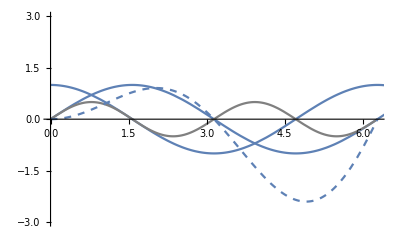

```mathematica
Show[ 
(*The sine*)Plot[Sin[x],{x,0,10Pi}, PlotRange->{{0,2Pi}, {-3,3}}],
(*The Cos*)Plot[Cos[x],{x,0,10Pi}, PlotRange->{{0,2Pi}, {-3,3}}],
(*The product Sin(x)cos(x) *)Plot[Sin[x]*Cos[x],{x,0,2Pi}, PlotRange->{{0,30}, {-3,3}}, PlotStyle->Gray],
(*the convolution*)Plot[(1/2)*x*Sin[x],{x,0,2Pi}, PlotStyle->Dashed, PlotRange->{{0,2Pi}, {-3,3}}],
ImageSize->Full]
```

Note that the convolution wave amplitude increases while the frequency remains constant

what woud happen if we examined the product

```mathematica
Animate[
Show[
Plot[Sin[x]*Cos[x-y],{x,0,4Pi}, PlotRange->{{0,4Pi}, {-2,2}}, PlotStyle->Dashed],
Plot[Sin[x]+Cos[x-y],{x,0,4Pi}, PlotRange->{{0,4Pi}, {-2,2}}, PlotStyle->Gray]
],
{y,0,2Pi,0.01}
]
```

## Convolution Sum

Rather than the product what if we used the sum

Given that:

```mathematica
f = Sin[#]&
```

Sin[#1]&

```mathematica
f[t]
```

Sin[t]

and:

```mathematica
g = Cos[#]&
```

Cos[#1]&

```mathematica
g[t]
```

Cos[t]

let us define the convolution of the two functions as 
∫f(τ)+*g(t-τ) ⅆτ

```mathematica
product = f[t-τ]g[τ]
```

Cos[τ] Sin[t-τ]

```mathematica
convolutionProduct =Integrate[product, {τ, 0,t}]
```

1/2 t Sin[t]

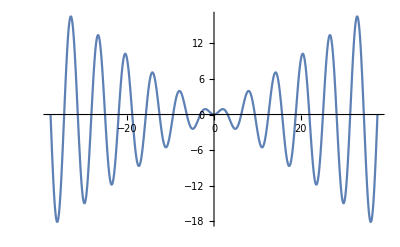

```mathematica
Plot[convolutionProduct,{t,-37.69911184307752,37.69911184307752}]
```

let us define the convolution of the two functions as 
∫f(τ)++g(t-τ) ⅆτ

```mathematica
sum = f[t-τ]+g[τ]
```

Cos[τ]+Sin[t-τ]

```mathematica
convolutionSum = Integrate[sum, {τ,0,t}]
```

1-Cos[t]+Sin[t]

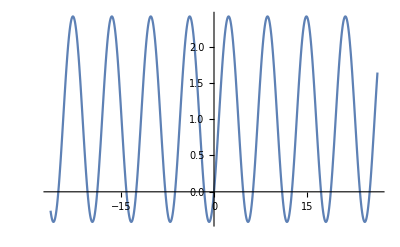

```mathematica
Plot[convolutionSum,{t,-26.389378290154262,26.389378290154262}]
```

let us define the convolution of the two functions as 
∫f(τ)+/g(t-τ) ⅆτ

let us define the convolution of the two functions as 
∫f(τ)++g(t-τ) ⅆτ

```mathematica
diff = f[t-τ]-g[τ]
```

-Cos[τ]+Sin[t-τ]

```mathematica
convolutionDiff = Integrate[diff, {τ,0,t}]
```

1-Cos[t]-Sin[t]

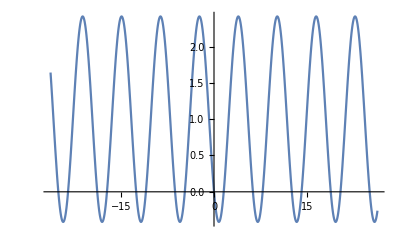

```mathematica
Plot[convolutionDiff,{t,-26.389378290154262,26.389378290154262}]
```

```mathematica
division = f[t-τ]/g[τ]
```

Sec[τ] Sin[t-τ]

```mathematica
convolutionDevide = Integrate[division, {τ,0,t}]
```

ConditionalExpression[Cos[t] Log[Cos[t]]+t Sin[t],Cos[t]≥0&&Re[t]>0&&Im[t]==0]

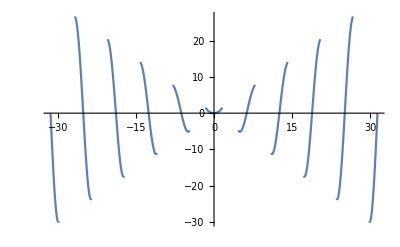

```mathematica
Plot[Cos[t] Log[Cos[t]]+t Sin[t], {t,-10Pi, 10Pi}]
```

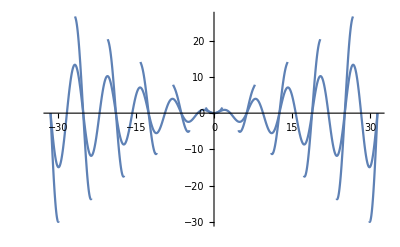

```mathematica
Show[
Plot[Cos[t] Log[Cos[t]]+t Sin[t], {t,-10Pi, 10Pi}],
Plot[convolutionProduct,{t,-10Pi, 10Pi}]
]
```